```mathematica
NormalizeData[symbol_,start_,end_]:=FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
PortfolioChart[stocks_,start_,end_]:=Module[{s,portfolio,data,symbols,std,return},
s=NormalizeData[#,start,end]&/@stocks;
portfolio=Transpose@{s[[1]][[All,1]],Mean/@Transpose@(#[[All,2]]&/@s)};
data=s~Join~{portfolio};
symbols=stocks~Join~{"portfolio"};
std=StandardDeviation@portfolio[[All,2]];
return=Last@portfolio[[All,2]];
{DateListPlot[data,PlotLegends->symbols,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All],{return,std,return/std}//TableForm[#,TableHeadings->{{"return","std","r/s"},Automatic}]&}
]
```

```mathematica
start=DatePlus[Today,-Quantity[5, "Years"]];
start1=DatePlus[Today,-Quantity[1, "Years"]];
start2=DatePlus[Today,-Quantity[2, "Years"]];
end=Today;
end//DateString
```

Wed 31 May 2017

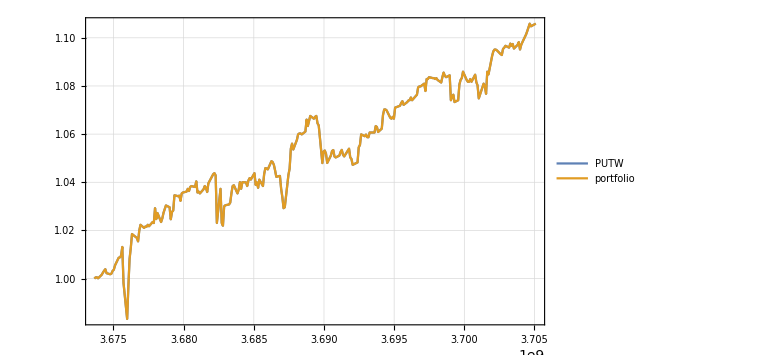
{-Graphics-,return | 1.10587
std | 0.0276315
r/s | 40.0223}

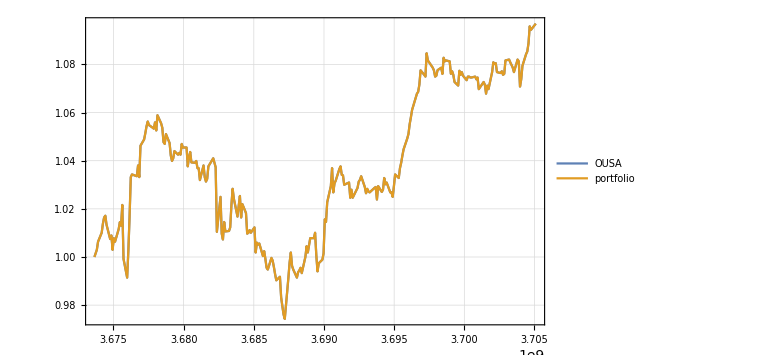
{-Graphics-,return | 1.09694
std | 0.0298501
r/s | 36.7484}

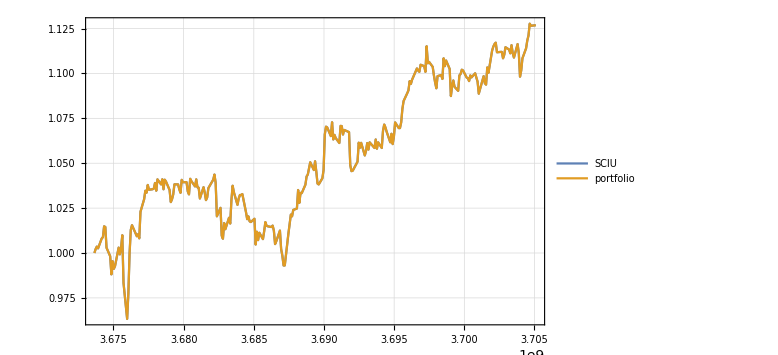
{-Graphics-,return | 1.12686
std | 0.0383309
r/s | 29.3982}

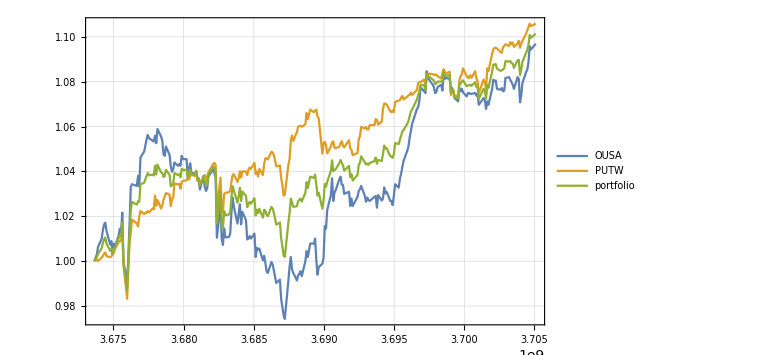
{-Graphics-,return | 1.10141
std | 0.0262431
r/s | 41.9695}

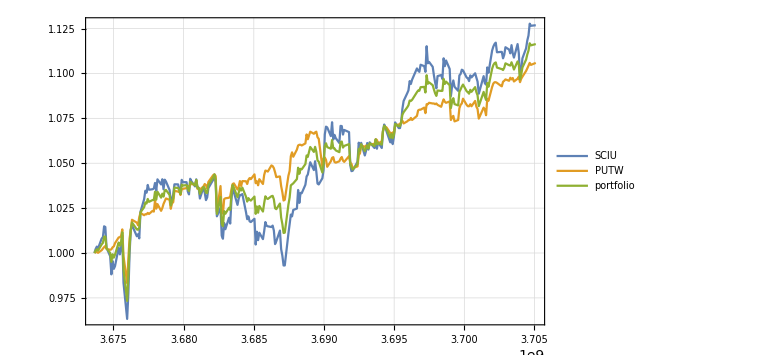
{-Graphics-,return | 1.11637
std | 0.0323187
r/s | 34.5424}

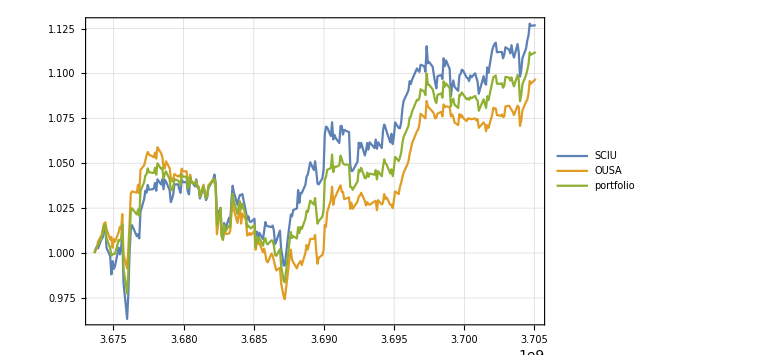
{-Graphics-,return | 1.1119
std | 0.0329294
r/s | 33.7662}

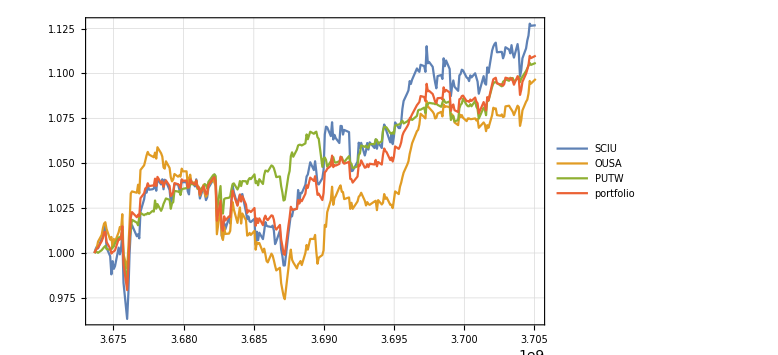
{-Graphics-,return | 1.10989
std | 0.0300858
r/s | 36.8909}

```mathematica
PortfolioChart[{"PUTW"},start1,end]
PortfolioChart[{"OUSA"},start1,end]
PortfolioChart[{"SCIU"},start1,end]
PortfolioChart[{"OUSA","PUTW"},start1,end]
PortfolioChart[{"SCIU","PUTW"},start1,end]
PortfolioChart[{"SCIU","OUSA"},start1,end]
PortfolioChart[{"SCIU","OUSA","PUTW"},start1,end]
```

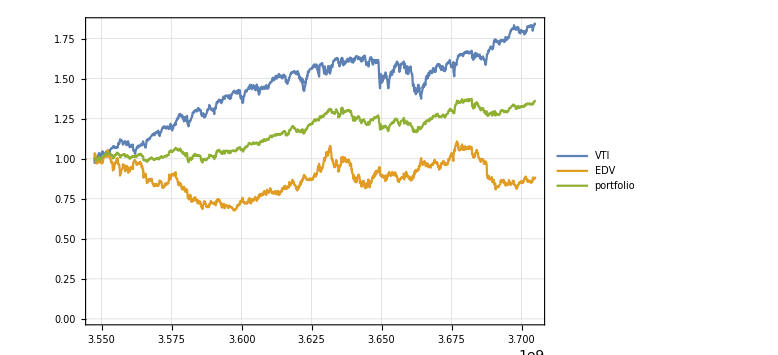
{-Graphics-,return | 1.36337
std | 0.121198
r/s | 11.2491}

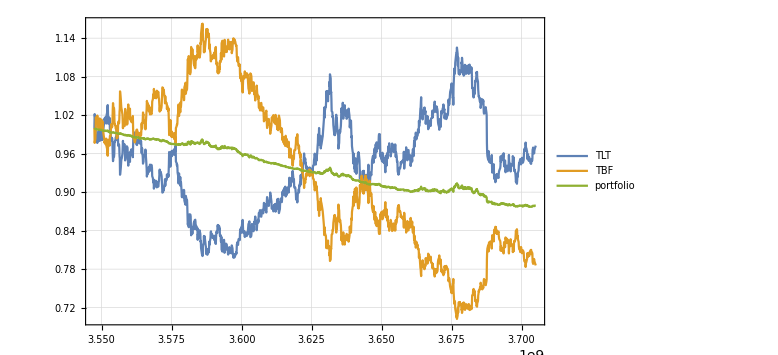
{-Graphics-,return | 0.879153
std | 0.0366047
r/s | 24.0175}

```mathematica
PortfolioChart[{"VTI","EDV"},start,end]
PortfolioChart[{"TLT","TBF"},start,end]
```

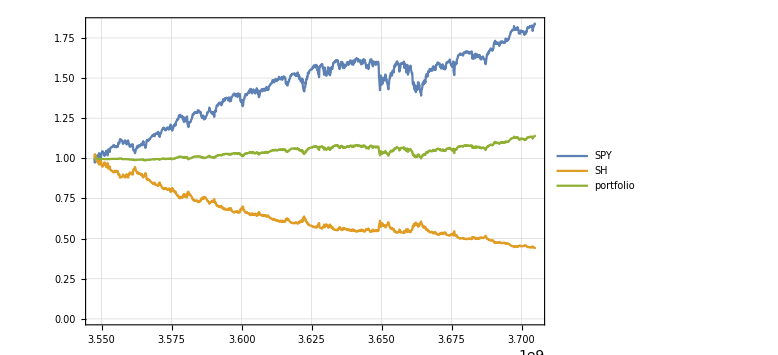
{-Graphics-,return | 1.13933
std | 0.0371016
r/s | 30.7085}

FinancialData::notent: RWM is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

Part::partd: Part specification FinancialData[RWM,{Day: ,Day: }]⟦All,1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {FinancialData[RWM,{Day: ,Day: }]⟦All,1⟧,{1.,1.02951,1.03128,1.01742,0.992535,0.998578,0.986136,«37»,0.975471,0.952364,0.944899,0.935656,0.936011,0.932101,«1207»}} cannot be transposed.

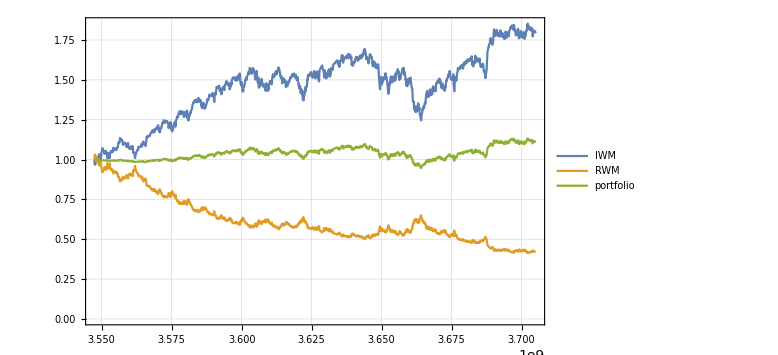
{-Graphics-,return | 1.10918
std | 0.0381076
r/s | 29.1066}

```mathematica
PortfolioChart[{"SPY","SH"},start,end]
PortfolioChart[{"IWM","RWM"},start,end]
```

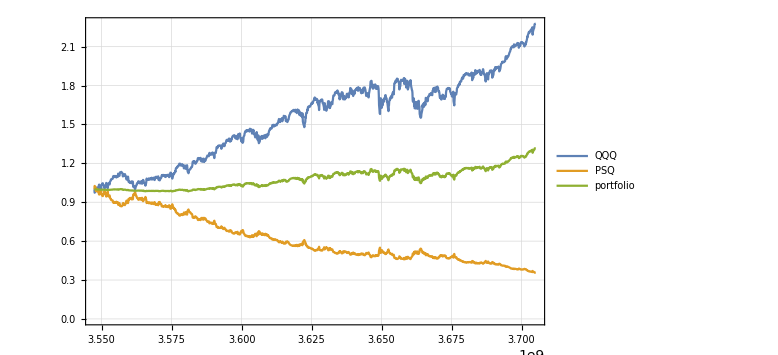
{-Graphics-,return | 1.31697
std | 0.0771288
r/s | 17.075}

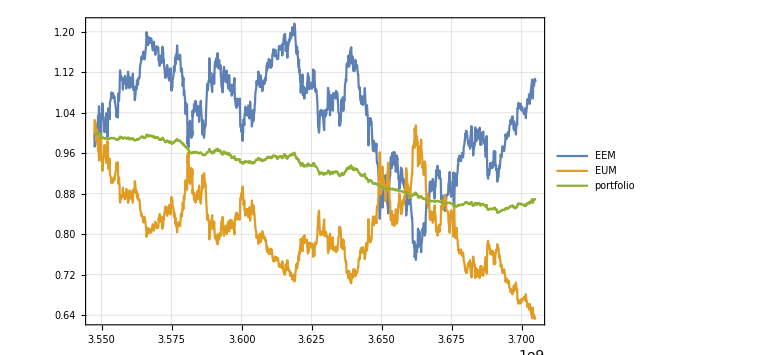
{-Graphics-,return | 0.868485
std | 0.0491348
r/s | 17.6756}

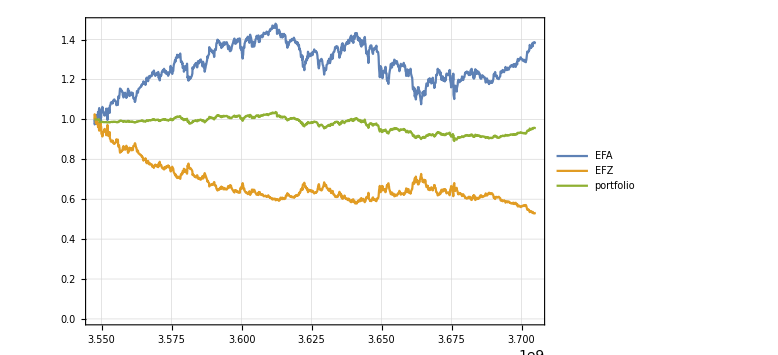
{-Graphics-,return | 0.956198
std | 0.0371922
r/s | 25.7096}

```mathematica
PortfolioChart[{"QQQ","PSQ"},start,end]
PortfolioChart[{"EEM","EUM"},start,end]
PortfolioChart[{"EFA","EFZ"},start,end]
```

FinancialData::notent: DUST is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

Part::partd: Part specification FinancialData[DUST,{Day: ,Day: }]⟦All,1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {FinancialData[DUST,{Day: ,Day: }]⟦All,1⟧,{1.,0.808064,0.768488,0.757711,0.751579,0.828688,0.81178,0.845596,«36»,1.00334,0.950576,0.888146,0.853029,0.86715,0.837421,«1207»}} cannot be transposed.

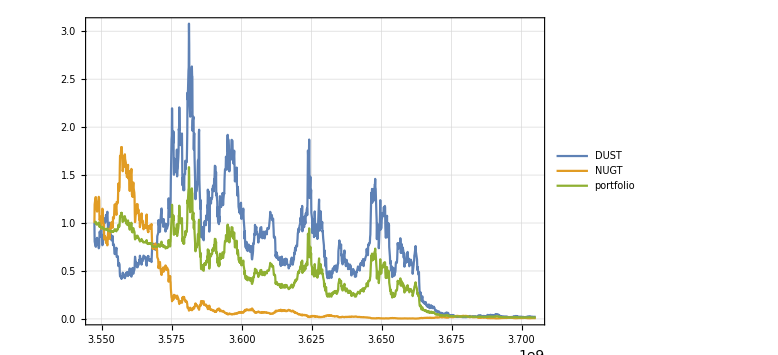
{-Graphics-,return | 0.015042
std | 0.341633
r/s | 0.0440298}

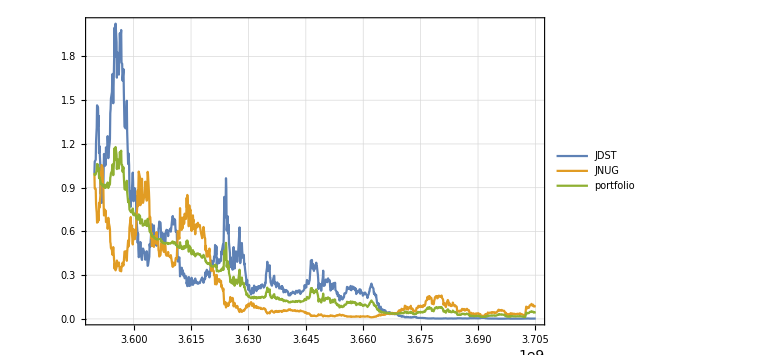
{-Graphics-,return | 0.043413
std | 0.286111
r/s | 0.151735}

```mathematica
PortfolioChart[{"DUST","NUGT"},start,end]
PortfolioChart[{"JDST","JNUG"},start,end]
```